Mathematica Code for Manuscript “Cell Swelling Under Metabolic Starvation Drives Solid Stress in Tumors” To reproduce Figure 5B
written by Mohammad Dehghany Dahaj
January 19, 2026

```mathematica
ClearAll["Global`*"];
$HistoryLength=0;
(*Reproducibility and I/O*)$Version ;(*records Mathematica version in the notebook kernel*)

SetDirectory@NotebookDirectory[];

outDir=FileNameJoin[{NotebookDirectory[],"output"}];
If[!DirectoryQ[outDir],CreateDirectory[outDir]];
```

```mathematica
(*Model Parameters*)par={ EE->9600,h->0.5 10^-6,σact->660,a0->8.8*10^-6,minr->8.8*10^-6,maxr->200* 10^-6,Rhol->0.05,Rhoe->0.4,x0->100,ν->0.5,RT->8.3145*310, pp0->0.002106,F->96500,cp0->150 ,cn0->110,gp->0.1,xO->40,w->0.15,Dc->2*10^-9,Po->72.3227,j->7*1.7*10^-7,Omega->3.0318*10^7,tau ->6*10^-3};
```

```mathematica
(*Model Equations*)
σcs:=(((ν+1)*a0^2-(b[r])^2*ν-(a[r])^2)*EE)/((2*ν^2-2)*a0^2)+σact;
Nct:=((a[r])^2+3 (b[r])^2)*Pi/(2 b[r])*σact+(-(2*ν+3)*(b[r])^4+(3*a0^2-(a[r])^2)*(ν+1)*(b[r])^2+(a[r])^2*((a0^2-(a[r])^2)*ν+a0^2))*Pi*EE/(4*a0^2*(ν^2-1)*b[r]);
rl=(6*Dc*Po/(j*Omega))^0.5/.par;
chi=(ArcCos[1-2*rl^2/maxr^2]-2*Pi)/3/.par;
rc=maxr*(0.5+Cos[chi])/.par;
rn=maxr*(0.5-Cos[chi])/.par;
PO2:=Piecewise[{{0,r<rn},{(Po+j*Omega/(6*Dc)*(r^2-maxr^2+2*rn^3*(1/r-1/maxr)))/. par//Simplify,r>=rn}}];
pp:=pp0/(1+ ⅇ^(5-PO2));
lambdap:=1+Rhoe+Rhol*ⅇ^(-( 1-r/maxr)/w);
ΔP:=RT*(ⅇ^(-(pp*F)/(2*gp*RT))*(ⅇ^((pp*F)/(gp*RT))*((x0*a0^3)/((b[r])^2*a[r]))^2+4*cn0*cp0)^0.5-cn0-cp0+(x0*a0^3)/((b[r])^2*a[r])-xO)/.par//Simplify;
bU:=a0/((1-u[r]/r)*(lambdap))/.par//Simplify;
aU:=a0/((1-u'[r])*(lambdap))/.par//Simplify;
σrU:= (2*h)/b[r]*σcs-ΔP/.a[r]->aU/.b[r]->bU//Simplify;
σθU:=(h*Nct)/(Pi*a[r]*b[r]) -ΔP /.a[r]->aU/.b[r]->bU//Simplify;
σrb:=2*tau/r+((2*h)/b[r]*σcs-ΔP)/.a[r]->aU/.b[r]->bU/.par/.r->maxr/.par//Simplify;
```

```mathematica
(*Solving the Equilibrium Equation(Eq.(1))*)
eq={D[σrU,r]+2/r(σrU-σθU)==0/.par,
u[0.001*minr/.par]==10^(-7),σrb== 0};
solU= NDSolve[eq,{u},{r,0.01*minr/.par,maxr/.par}];
```

FindRoot::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the function value is still greater than the tolerance prescribed by the AccuracyGoal option.

NDSolve::berr: The scaled boundary value residual error of 42437.6 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

```mathematica
(*Calculation of Pressure Difference, Ion Concentrations, and Membrane Potential*)
ΔPU:=ΔP/.a[r]->aU/.b[r]->bU//Simplify;
cn:=-((x0*a0^3)/((b[r])^2*a[r]))/2+(ⅇ^(-(pp*F)/(2*gp*RT))*(ⅇ^((pp*F)/(gp*RT))*((x0*a0^3)/((b[r])^2*a[r]))^2+4*cn0*cp0)^0.5)/2/.a[r]->aU/.b[r]->bU//Simplify;
cp:=cn+(x0*a0^3)/((b[r])^2*a[r])/.a[r]->aU/.b[r]->bU//Simplify;
ϕ:=-RT/F*Log[cn0/cn]/.a[r]->aU/.b[r]->bU//Simplify;
x:=(x0*a0^3)/((b[r])^2*a[r])/.a[r]->aU/.b[r]->bU//Simplify;
```

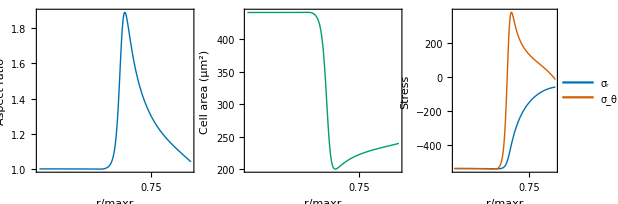

```mathematica
(*Plots of the Cell Aspect Ratio, Cell Area, and Radial and Tangential Components of the Solid Stress Field*)
col=<|"blue"->RGBColor["#0072B2"],"orange"->RGBColor["#D55E00"],"green"->RGBColor["#009E73"]|>;

$labelStyle=Directive[Black,16,FontFamily->"Helvetica"];
$tickStyle=Directive[Black,14];
$frameStyle=Directive[Black,AbsoluteThickness[1.5]];
$imgSize=800;

(*Left& bottom ticks only;normalized bottom ticks 0:0.25:1*)
normTicks={{Automatic,None},(*left,right*){{{0,0},{.25,.25},{.5,.5},{.75,.75},{1,1}},None}  (*bottom,top*)};

basePlotOpts={Axes->False,Frame->True,FrameStyle->$frameStyle,FrameTicks->normTicks,FrameTicksStyle->$tickStyle,LabelStyle->$labelStyle,BaseStyle->{FontFamily->"Helvetica"},ImageSize->$imgSize,PlotRange->All};

(*------------Normalized radius helpers------------*)
rminNorm=N[(minr/. par)/(maxr/. par)];
rmax=(maxr/. par);

(*Model evaluators on rnorm∈[rminNorm,1]*)
arModel[rnorm_]:=Evaluate[(bU/aU)/. r->rnorm*rmax/. par/. solU[[1]]];
areaModel[rnorm_]:=Evaluate[(Pi*bU*aU*10^12)/. r->rnorm*rmax/. par/. solU[[1]]]; (*μm^2*)
sigmarModel[rnorm_]:=Evaluate[(σrU)/. r->rnorm*rmax/. par/. solU[[1]]];
sigmatModel[rnorm_]:=Evaluate[(σθU)/. r->rnorm*rmax/. par/. solU[[1]]];
PotentialModel[rnorm_]:=Evaluate[(ϕ)/. r->rnorm*rmax/. par/. solU[[1]]];
(*------------Panel A:Aspect Ratio vs r/maxr------------*)
figAR=Plot[arModel[rnorm],{rnorm,rminNorm,1},Evaluate@basePlotOpts,PlotStyle->Directive[col["blue"],Thick],AspectRatio->1,FrameLabel->{"r/maxr","Aspect ratio"},PlotRange->{{0,1},All}];
(*------------Panel B:Cell Area vs r/maxr------------*)
figArea=Plot[areaModel[rnorm],{rnorm,rminNorm,1},Evaluate@basePlotOpts,PlotStyle->Directive[col["green"],Thick],AspectRatio->1,FrameLabel->{"r/maxr",Row[{"Cell area (",Superscript["μm",2],")"}]},PlotRange->{{0,1},All}];
(*------------Panel C:Radial& Tangential Stresses vs r/maxr------------*)
figStress=Plot[{sigmarModel[rnorm],sigmatModel[rnorm]},{rnorm,rminNorm,1},Evaluate@basePlotOpts,PlotStyle->{Directive[col["blue"],Thick],Directive[col["orange"],Thick]},AspectRatio->1,FrameLabel->{"r/maxr","Stress"},Epilog->Inset[LineLegend[{Directive[col["blue"],Thick],Directive[col["orange"],Thick]},{Style[Subscript[σ,r],16],Style[Subscript[σ,θ],16]},LegendLayout->"Column",LegendMarkerSize->18,LabelStyle->$labelStyle],Scaled[{0.1,0.9}],{Left,Top}]];
(*------------Combined figure row------------*)
finalRow=GraphicsRow[{figAR,figArea,figStress},Spacings->6];
finalRow
```